```mathematica
(* IMPORT MODULES *)
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
```

```mathematica
(* INITIALIZING PARAMETERS *)
uq=0.2848 (* up quark mass *);
sq=0.5553 (* strange quark mass *);
cq=1.8182 (* charm quark mass *);
bq=5.2019 (* bottom quark mass *);
sigma=0.154/2; (* coefficient of string strength term *)
alphaCoulomb=0; (* coefficient of Coulomb term (0.0175) if you want to replicate Bucks *)
Cqqq=-1.4204(* V = -Subscript[α, C]/r + σr + Subscript[C, qqq] *);
```

```mathematica
(* INITIALIZING HYPERPARAMETERS *)
γMax=4;
Λ=0;
m1=uq;
m2=uq;
m3=cq;
t1=tMatrix[Λ,γMax,1];
t2=tMatrix[Λ,γMax,2];
size=Dimensions[t1][[1]];
```

```mathematica
kMatrix[0,4,1]//MatrixForm
```

(1.5 | 0.612372 | 0. | 0.612372 | 0. | 0. | 0. | 0. | 0. | 0.
0.612372 | 2.5 | 0. | 0. | 1.11803 | 0. | 0. | 0.612372 | 0. | 0.
0. | 0. | 2.5 | 0. | 0. | 0.790569 | 0. | 0. | 0.790569 | 0.
0.612372 | 0. | 0. | 2.5 | 0. | 0. | 0. | 0.612372 | 0. | 1.11803
0. | 1.11803 | 0. | 0. | 3.5 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.790569 | 0. | 0. | 3.5 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 3.5 | 0. | 0. | 0.
0. | 0.612372 | 0. | 0.612372 | 0. | 0. | 0. | 3.5 | 0. | 0.
0. | 0. | 0.790569 | 0. | 0. | 0. | 0. | 0. | 3.5 | 0.
0. | 0. | 0. | 1.11803 | 0. | 0. | 0. | 0. | 0. | 3.5)

```mathematica
(* THIS FUNCTION RETURNS THE BARYON HAMILTONIAN FOR A GIVEN ω *)
baryonHamiltonian[ω_]:=(
omega=ω;
vCoulomb=polynomialOperator[Λ,γMax,-1];
vLinear=polynomialOperator[Λ,γMax,1];
v12baryon=-alphaCoulomb*α*vCoulomb+(sigma*vLinear)/α;
v23baryon=-alphaCoulomb*α1*(Transpose[t1].vCoulomb.t1)+(sigma*(Transpose[t1].vLinear.t1))/α1;
v31baryon=-alphaCoulomb*α2*(Transpose[t2].vCoulomb.t2)+(sigma*(Transpose[t2].vLinear.t2))/α2;
kin=kMatrix[Λ,γMax,ω];
mas1=IdentityMatrix[size]*m1;
mas2=IdentityMatrix[size]*m2;
mas3=IdentityMatrix[size]*m3;
cqqq=IdentityMatrix[size]*(Cqqq);
Hbaryon=mas1+mas2+mas3+kin+v12baryon+v23baryon+v31baryon+cqqq)
```

```mathematica
baryonHamiltonian[1]//MatrixForm
```

(3.9674-1.5/ω+0.580436/(√ω) | 0.+0.612372/ω-0.0811629/(√ω) | 0. | 0.+0.612372/ω-0.155799/(√ω) | 0.-0.0103032/(√ω) | 0.+(5.20417×10^-18)/(√ω) | 0.-0.0128115/(√ω) | 0.-0.0143237/(√ω) | 0.-(4.33681×10^-18)/(√ω) | 0.-0.0269923/(√ω)
0.+0.612372/ω-0.0811629/(√ω) | 5.9674-2.5/ω+0.694164/(√ω) | 0.-(1.73472×10^-17)/(√ω) | 0.-0.0143237/(√ω) | 0.+1.11803/ω-0.121696/(√ω) | 0.+(6.93889×10^-18)/(√ω) | 0.+0.0120132/(√ω) | 0.+0.612372/ω-0.142368/(√ω) | 0.+(1.2902×10^-17)/(√ω) | 0.-0.00415368/(√ω)
0. | 0.-(2.77556×10^-17)/(√ω) | 5.9674-2.5/ω+0.745267/(√ω) | 0.+(2.77556×10^-17)/(√ω) | 0. | 0.+0.790569/ω-0.0811354/(√ω) | 0.+(1.38778×10^-17)/(√ω) | 0.-(6.93889×10^-18)/(√ω) | 0.+0.790569/ω-0.154539/(√ω) | 0.-(4.33681×10^-18)/(√ω)
0.+0.612372/ω-0.155799/(√ω) | 0.-0.0143237/(√ω) | 0.+(3.46945×10^-17)/(√ω) | 5.9674-2.5/ω+0.785574/(√ω) | 0.-0.00545493/(√ω) | 0.-(4.33681×10^-18)/(√ω) | 0.+0.0141381/(√ω) | 0.+0.612372/ω-0.065356/(√ω) | 0. | 0.+1.11803/ω-0.225197/(√ω)
0.-0.0103032/(√ω) | 0.+1.11803/ω-0.121696/(√ω) | 0. | 0.-0.00545493/(√ω) | 7.9674-3.5/ω+0.783828/(√ω) | 0.+(2.77556×10^-17)/(√ω) | 0.+0.000924671/(√ω) | 0.-0.014657/(√ω) | 0.+(2.5804×10^-17)/(√ω) | 0.-0.00263643/(√ω)
0.+(5.20417×10^-18)/(√ω) | 0. | 0.+0.790569/ω-0.0811354/(√ω) | 0. | 0.-(6.93889×10^-18)/(√ω) | 7.9674-3.5/ω+0.838514/(√ω) | 0.-(1.73472×10^-17)/(√ω) | 0.-(5.55112×10^-17)/(√ω) | 0.-0.0162752/(√ω) | 0.-(1.73472×10^-17)/(√ω)
0.-0.0128115/(√ω) | 0.+0.0120132/(√ω) | 0.-(1.38778×10^-17)/(√ω) | 0.+0.0141381/(√ω) | 0.+0.000924671/(√ω) | 0.+(1.73472×10^-17)/(√ω) | 7.9674-3.5/ω+0.89111/(√ω) | 0.-0.0164013/(√ω) | 0.-(3.46945×10^-17)/(√ω) | 0.-0.000500779/(√ω)
0.-0.0143237/(√ω) | 0.+0.612372/ω-0.142368/(√ω) | 0. | 0.+0.612372/ω-0.065356/(√ω) | 0.-0.014657/(√ω) | 0.-(3.46945×10^-17)/(√ω) | 0.-0.0164013/(√ω) | 7.9674-3.5/ω+0.880964/(√ω) | 0.+(1.38778×10^-17)/(√ω) | 0.-0.0162507/(√ω)
0.-(4.33681×10^-18)/(√ω) | 0.+(8.67362×10^-18)/(√ω) | 0.+0.790569/ω-0.154539/(√ω) | 0. | 0.+(8.67362×10^-18)/(√ω) | 0.-0.0162752/(√ω) | 0.-(2.77556×10^-17)/(√ω) | 0. | 7.9674-3.5/ω+0.908151/(√ω) | 0.-(2.08167×10^-17)/(√ω)
0.-0.0269923/(√ω) | 0.-0.00415368/(√ω) | 0. | 0.+1.11803/ω-0.225197/(√ω) | 0.-0.00263643/(√ω) | 0.+(8.67362×10^-18)/(√ω) | 0.-0.000500779/(√ω) | 0.-0.0162507/(√ω) | 0.-(2.77556×10^-17)/(√ω) | 7.9674-3.5/ω+0.945542/(√ω))

```mathematica
(* Optimises the lowest lying eigenvalue (searches for best ω) *)
baryonMinimumEigenvalue[gammaMax_,Lambda_,mass1_,mass2_,mass3_]:=(
γMax=gammaMax;
Λ=Lambda;
m1=mass1;
m2=mass2;
m3=mass3;
t1=tMatrix[Λ,gammaMax,1]; (* transformation matrix 1 *)
t2=tMatrix[Λ,gammaMax,2];(* transformation matrix 2 *)
size=Dimensions[t1][[1]]; (* size of matrix *)
Min[Table[Eigenvalues[baryonHamiltonian[ω]][[-1]],{ω,0.1,0.6,0.01}]])
```

```mathematica
h=baryonHamiltonian[0.35];
Eigensystem[h]
```

{{3.79897,3.73404,3.72688,3.68107,3.63972,3.56913,3.15278,3.06557,2.96283,2.456},{{-0.0287551,0.00226225,-9.11876×10^-17,-0.0216361,0.0116701,-6.95482×10^-16,0.0645059,-0.256717,2.23436×10^-15,0.963587},{-1.2777×10^-15,-8.69028×10^-15,0.0313782,1.07409×10^-14,-1.65154×10^-14,0.24945,-5.98572×10^-14,6.45062×10^-14,-0.967879,2.40103×10^-14},{0.0183665,0.0995522,1.56074×10^-15,-0.113047,0.18221,1.72839×10^-14,0.650484,-0.68386,-9.21044×10^-14,-0.230169},{0.0380651,0.0558998,3.20523×10^-15,-0.168889,0.155585,1.31159×10^-14,-0.754323,-0.600548,2.1798×10^-15,-0.114171},{3.87396×10^-16,2.02918×10^-15,-0.250056,-1.88197×10^-15,1.0651×10^-14,-0.935603,-1.43512×10^-14,-1.09718×10^-15,-0.249238,3.91942×10^-16},{-0.0031463,0.293296,2.83618×10^-15,0.0290349,0.918854,9.23158×10^-15,-0.00780984,0.255876,3.37388×10^-15,0.0574338},{-0.071912,-0.100243,1.54818×10^-16,0.968353,0.0583471,-4.60537×10^-16,-0.0518934,-0.20008,-1.26405×10^-16,-0.0307051},{-2.30435×10^-16,-2.13683×10^-15,0.967723,-5.9341×10^-16,3.21996×10^-16,-0.249845,-2.41867×10^-16,-2.76473×10^-17,-0.0330189,0.},{-0.144542,-0.932341,-1.78422×10^-15,-0.126721,0.304836,1.59608×10^-15,0.0245618,-0.00973257,-1.57198×10^-16,-0.0128989},{-0.985552,0.147064,3.20191×10^-17,-0.0601633,-0.0428339,-4.68129×10^-17,-0.018685,-0.0132395,-3.09668×10^-16,-0.0328644}}}

```mathematica
baryonList={{uq,uq,uq},{uq,uq,cq},{uq,uq,bq},{uq,sq,cq},{uq,sq,bq},{uq,cq,cq},{uq,cq,bq},{uq,bq,bq},{bq,cq,cq},{cq,cq,cq},{bq,bq,cq},{bq,bq,bq}};
```

```mathematica
For[index=1,index≤Length[baryonList],index++,
Print[index];
Print[baryonList[[index,1]]];
Print[baryonList[[index,2]]];
Print[baryonList[[index,3]]];
Print[Table[baryonMinimumEigenvalue[γMax,1,baryonList[[index,1]],baryonList[[index,2]],baryonList[[index,3]]],{γMax,1,7,2}]]]
```

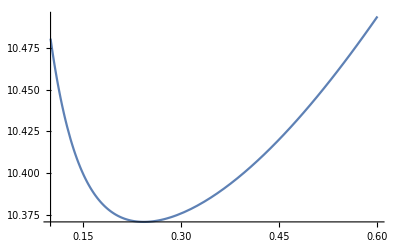

{{5.93237,0.1},{5.90381,0.11},{5.88171,0.12},{5.86459,0.13},{5.8513,0.14},{5.84101,0.15},{5.83305,0.16},{5.8269,0.17},{5.82215,0.18},{5.81851,0.19},{5.8157,0.2},{5.81355,0.21},{5.8119,0.22},{5.81062,0.23},{5.80964,0.24},{5.80889,0.25},{5.8083,0.26},{5.80784,0.27},{5.80749,0.28},{5.80721,0.29},{5.807,0.3},{5.80684,0.31},{5.80672,0.32},{5.80664,0.33},{5.80661,0.34},{5.8066,0.35},{5.80663,0.36},{5.8067,0.37},{5.80681,0.38},{5.80695,0.39},{5.80714,0.4},{5.80738,0.41},{5.80766,0.42},{5.808,0.43},{5.80839,0.44},{5.80884,0.45},{5.80935,0.46},{5.80992,0.47},{5.81055,0.48},{5.81125,0.49},{5.81202,0.5},{5.81286,0.51},{5.81377,0.52},{5.81476,0.53},{5.81582,0.54},{5.81695,0.55},{5.81816,0.56},{5.81944,0.57},{5.8208,0.58},{5.82224,0.59},{5.82375,0.6}}

```mathematica
Plot[Eigenvalues[baryonHamiltonian[ω]][[-1]],{ω,0.1,0.6}]
```